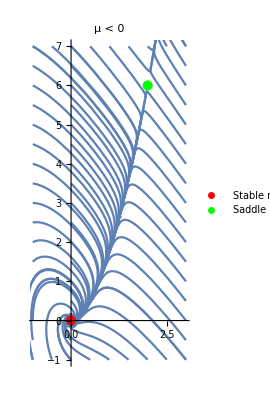

```mathematica
Clear["Global`*"]
minx=-1; maxx=3; miny=-1;  maxy=7; μ=-1;
sol = Solve[{0 == μ*x+y-x^2, 0 == -x+μ*y+2 x^2}, {x,y}];
s[x0_,y0_]:=NDSolve[{x'[t]==μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==x0, y[0]==y0},{x,y},{t,0,10}];
initialCondition=Join[Table[{0,y},{y,miny,maxy,0.5}],Table[{minx,y},{y,miny,maxy,0.5}],Table[{maxx,y},{y,miny,maxy,0.5}],Table[{x,miny},{x,minx,maxx,0.5}],Table[{x,maxy},{x,minx,maxx,0.5}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,0,10}, PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.05,0.05,0.05,0.05,0.}],Arrow[x]},ListPlot[{{sol[[1, 1, 2]],sol[[1, 2, 2]]}}, PlotMarkers-> {Automatic, 10}, PlotStyle-> {Red}, PlotLegends->{"Stable node"}],
ListPlot[{{sol[[2, 1, 2]],sol[[2, 2, 2]]}}, PlotMarkers-> {Automatic, 10}, PlotStyle-> {Green}, PlotLegends->{"Saddle point"}],
PlotLabel-> "μ < 0"]
```

NDSolve::nderr: Error test failure at t == 27.3062; unable to continue.

NDSolve::nderr: Error test failure at t == 27.6476; unable to continue.

NDSolve::nderr: Error test failure at t == 27.9415; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

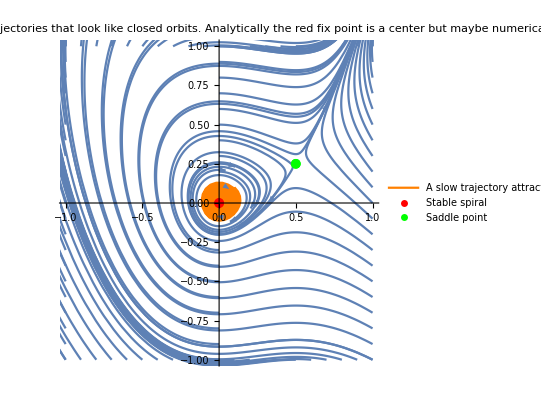

```mathematica
minx=-1; maxx=1; miny=-1;  maxy=1; μ=0;
sol = Solve[{0 == μ*x+y-x^2, 0 == -x+μ*y+2 x^2}, {x,y}];
s[x0_,y0_]:=NDSolve[{x'[t]==μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==x0, y[0]==y0},{x,y},{t,0,1000}];
initialCondition=Join[Table[{0,y},{y,miny,maxy,0.1}],Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,0,10}, PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.}],Arrow[x]},
ParametricPlot[Evaluate[{x[t], y[t]} /. s[0.1, 0.1],{t, 0, 1000}], PlotRange->{{minx,maxx},{miny,maxy}}, PlotStyle->{Orange}, PlotLegends->{"A slow trajectory attracted to fixpoint (0,0)."}], 
ListPlot[{{sol[[1, 1, 2]],sol[[1, 2, 2]]}}, PlotMarkers-> {Automatic, 10}, PlotStyle-> {Red}, PlotLegends->{"Stable spiral"}],
ListPlot[{{sol[[2, 1, 2]],sol[[2, 2, 2]]}}, PlotMarkers-> {Automatic, 10}, PlotStyle-> {Green}, PlotLegends->{"Saddle point"}],
PlotLabel-> "μ = 0, stable sprial with trajectories that look like closed orbits. Analytically the red fix point is a center but maybe numerical errors?"]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::nderr: Error test failure at t == 26.7861; unable to continue.

NDSolve::nderr: Error test failure at t == 27.1401; unable to continue.

NDSolve::nderr: Error test failure at t == 27.6008; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndcf: Repeated convergence test failure at t == 23.5083; unable to continue.

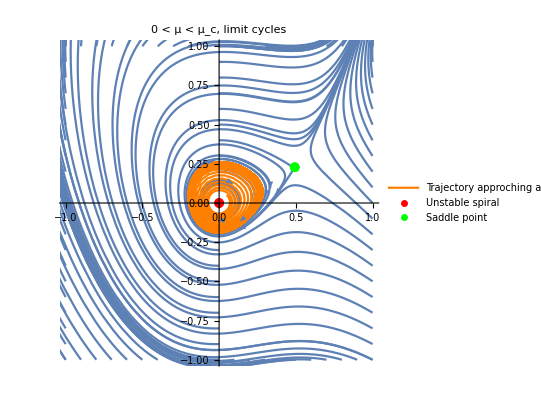

```mathematica
minx=-1; maxx=1; miny=-1;  maxy=1;μ=0.03;
sol = Solve[{0 == μ*x+y-x^2, 0 == -x+μ*y+2 x^2}, {x,y}];
s[x0_,y0_]:=NDSolve[{x'[t]==μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==x0, y[0]==y0},{x,y},{t,0,1000}];
initialCondition=Join[Table[{0,y},{y,miny,maxy,0.1}],Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,0,10}, PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.}],Arrow[x]},
ParametricPlot[Evaluate[{x[t], y[t]} /. s[0.05, 0.05],{t, 0, 1000}], PlotRange->{{minx,maxx},{miny,maxy}}, PlotStyle->{Orange}, PlotLegends->{"Trajectory approching a limit cycle"}], 
ListPlot[{{sol[[1, 1, 2]],sol[[1, 2, 2]]}}, PlotMarkers-> {Automatic, 10}, PlotStyle-> {Red}, PlotLegends->{"Unstable spiral"}],
ListPlot[{{sol[[2, 1, 2]],sol[[2, 2, 2]]}}, PlotMarkers-> {Automatic, 10}, PlotStyle-> {Green}, PlotLegends->{"Saddle point"}],
PlotLabel-> "0 < μ < μ_c, limit cycles"]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::nderr: Error test failure at t == 26.5222; unable to continue.

NDSolve::nderr: Error test failure at t == 26.5334; unable to continue.

NDSolve::nderr: Error test failure at t == 26.6859; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

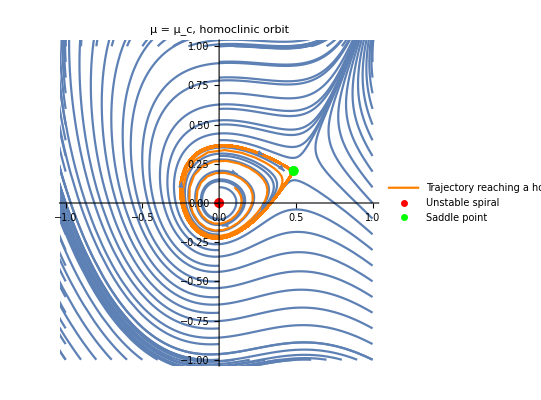

```mathematica
minx=-1; maxx=1; miny=-1;  maxy=1;μ=0.066;
sol = Solve[{0 == μ*x+y-x^2, 0 == -x+μ*y+2 x^2}, {x,y}];
s[x0_,y0_]:=NDSolve[{x'[t]==μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==x0, y[0]==y0},{x,y},{t,0,1000}];
initialCondition=Join[Table[{0,y},{y,miny,maxy,0.1}],Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,0,10}, PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.}],Arrow[x]},
ParametricPlot[Evaluate[{x[t], y[t]} /. s[0.1, 0.1],{t, 0, 1000}], PlotRange->{{minx,maxx},{miny,maxy}}, PlotStyle->{Orange},PlotLegends->{"Trajectory reaching a homoclinic orbit"}],
ListPlot[{{sol[[1, 1, 2]],sol[[1, 2, 2]]}}, PlotMarkers-> {Automatic, 10}, PlotStyle-> {Red}, PlotLegends->{"Unstable spiral"}],
ListPlot[{{sol[[2, 1, 2]],sol[[2, 2, 2]]}}, PlotMarkers-> {Automatic, 10}, PlotStyle-> {Green}, PlotLegends->{"Saddle point"}],
PlotLabel-> "μ = μ_c, homoclinic orbit"]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NDSolve::nderr: Error test failure at t == 24.1416; unable to continue.

NDSolve::nderr: Error test failure at t == 24.2349; unable to continue.

NDSolve::nderr: Error test failure at t == 24.6014; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

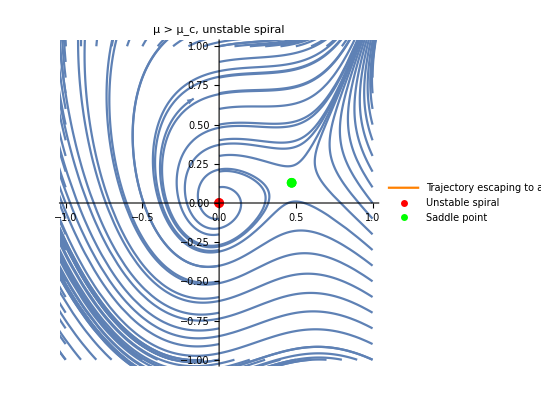

```mathematica
minx=-1; maxx=1; miny=-1;  maxy=1;μ=0.2;
sol = Solve[{0 == μ*x+y-x^2, 0 == -x+μ*y+2 x^2}, {x,y}];
s[x0_,y0_]:=NDSolve[{x'[t]==μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==x0, y[0]==y0},{x,y},{t,0,100}];
initialCondition=Join[Table[{0,y},{y,miny,maxy,0.1}],Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,0,10}, PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.}],Arrow[x]},
ParametricPlot[Evaluate[{x[t], y[t]} /. s[0.01, 0.01],{t, 0, 100}], PlotRange->{{minx,maxx},{miny,maxy}}, PlotStyle->{Orange},PlotLegends->{"Trajectory escaping to a unstable manifold of the saddle point"}],
ListPlot[{{sol[[1, 1, 2]],sol[[1, 2, 2]]}}, PlotMarkers-> {Automatic, 10}, PlotStyle-> {Red}, PlotLegends->{"Unstable spiral"}],
ListPlot[{{sol[[2, 1, 2]],sol[[2, 2, 2]]}}, PlotMarkers-> {Automatic, 10}, PlotStyle-> {Green}, PlotLegends->{"Saddle point"}],
PlotLabel-> "μ > μ_c, unstable spiral"]
```

```mathematica
s=.
sol=DSolve[{x'[t]==u*x[t],x[0]==γ},x[t],t]//Flatten
```

{x[t]→ⅇ^(t u) γ}

```mathematica
Clear["Global`*"]
f[x_,y_]:=μ*x+y-x^2;
g[x_,y_]:=-x+μ*y+2 x^2;
sol=Solve[f[x,y]==0&&g[x,y]==0,{x,y}];
J[x_,y_]:={{D[f[x,y],x],D[f[x,y],y]},{D[g[x,y],x],D[g[x,y],y]}};
eval=J[x,y]/. sol[[2]]//Eigenvalues
u = eval[[2]]
```

{(-1+2 μ-√(5+9 μ^2+4 μ^3+μ^4))/(2+μ),(-1+2 μ+√(5+9 μ^2+4 μ^3+μ^4))/(2+μ)}

(-1+2 μ+√(5+9 μ^2+4 μ^3+μ^4))/(2+μ)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

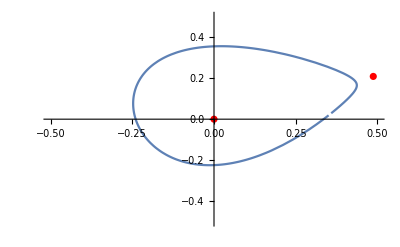

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.413465

-5.116

-0.883183

```mathematica
Clear["Global`*"]
criticalMu = 0.066;
μ = 0.060;
tMin = 170;
tMax = tMin-0.1+9.8624007122786;
f[x_,y_]:=μ x + y -x^2 ;
g[x_,y_]:=-x + μ y +2x^2;
fp = Solve[{f[x,y]==0, g[x,y]==0}, {x,y}];
data={{fp[[1,1,2]],fp[[1,2,2]]},{fp[[2,1,2]],fp[[2,2,2]]}};
line =  Fit[data,{1,x},x];
p1 = ListPlot[data,PlotStyle->Red];
s=NDSolve[{x'[t]==μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==y[0]==0.1},{x,y},{t,tMin,tMax}];
p3= ParametricPlot[Evaluate[{x[t],y[t]}/. s],{t,tMin,tMax},PlotRange->{{-1,1},{-1,1}}] ;
Show[p1,p3,PlotRange->{{-0.5,0.5},{-0.5,0.5}}]
tIntersect = Solve[{y[t]==fp[[2,2,2]]}/.s[[1,2]],t][[1,1,2]];
xIf = s[[1,1,2]];
γ = xIf[tIntersect]
xVal = Log[Abs[μ-criticalMu]]
yVal = Log[γ]
```

```mathematica
plotData = {{-5.115995809754081,-0.8831824175751058},{-5.115995809754081, -0.8831824175751058},{-5.521460917862245,-0.8397348233958074},{-5.809142990314027,-0.8169247714703272},{-6.2146080984221905,-1.6161665232963962},{-6.2146080984221905,-1.6161665232963962},{-6.2146080984221905,-1.6161665232963962}};
line2 =  Fit[plotData,{1,x},x]
gammaPlot = Show[ListPlot[plotData,PlotStyle->Red],Plot[line2,{x,-10,0},PlotLegends->{"log(γ) vs. log|μ-μ_c|, y = 2.8 + 0.7 x"}],PlotRange->{{-10,0},{-5,5}}];
```

2.78486+0.690574 x

```mathematica
tConst = 0;
f=s[[1,1,2]];
g =s[[1,2,2]];
xStart = s[[1,1,2]][tMin];
yStart = s[[1,2,2]][tMin];
temp=FindRoot[f[t]+ g[t]==xStart+yStart,{t,tMin+tConst}];

xStart
s[[1,1,2]][temp[[1,2]]]
yStart
s[[1,2,2]][temp[[1,2]]]
tPeriod = Abs[tMin-temp[[1,2]]];
{Abs[μ-criticalMu], tPeriod}
```

0.350527

0.350527

0.0186812

0.0186812

{0.006,0.}

```mathematica
plotDataPeriodTime = {{0.006,9.8624},{0.005,10.1301},{0.004,10.4571}, {0.003,10.8774},{0.002,11.4664},{0.001,12.4583}};
logPlotDataPeriodTime = Log[plotDataPeriodTime];
line3 =  Fit[logPlotDataPeriodTime,{1,x},x]
periodPlot = Show[ListPlot[logPlotDataPeriodTime,PlotStyle->Red],Plot[line3,{x,-10,0},PlotStyle->Orange,PlotLegends->{"log(Tμ) vs. log|μ-μ_c|, y = 1.6 - 0.1 x"}],PlotRange->{{-10,0},{-5,5}}];
```

1.62606-0.130313 x

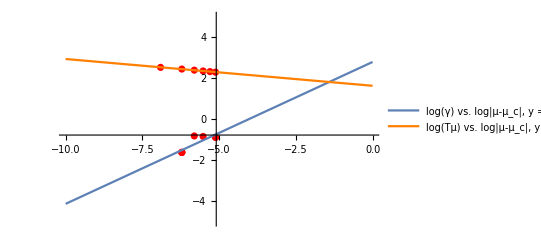

```mathematica
Show[gammaPlot, periodPlot, PlotRange->{{-10,0},{-5,5}}]
```